When accounting for the Fresnel term, we end up with the BRDF being written as:

	ρ_r(ω_i,ω_o)=ρ_d/π[1-F(ω_i,n)] + F(ω_i,n).ρ_s(ω_i,ω_o)

With ρ_s(ω_i,ω_o) the specular BRDF we won’t talk about and F(ω_i,n) the Schlick’s approximation for the Fresnel term:

	F(ω_i,n) = F_0+(1-F_0)(1-ω_i·n)^5
	
Focusing on the diffuse part we obtain the diffuse integral:

	L(ω_o)=ρ_d/π L(ω_i)∫(1-F( cos(θ))) (ω_i·n) sin(θ)ⅆθ
	=ρ_d/π L(ω_i)[∫(1-F_0) (ω_i·n)  sin(θ)ⅆθ-∫(1-F_0) (1-ω_i·n)^5(ω_i·n) sin(θ)ⅆθ]
	=ρ_d/π K_0[∫ (ω_i·n) sin(θ)ⅆθ-∫ (1-ω_i·n)^5(ω_i·n)sin(θ)ⅆθ]
		
Where K_0=1-F_0 the complement to the orthogonal Fresnel term.

The first integral term is our classical result that separates into n_x and n_y terms:
	∫ (ω_i·n) sin(θ)ⅆθ =  n_x∫ sin(θ) sin(θ)ⅆθ+n_y∫ cos(θ) sin(θ)ⅆθ
= n_x/2[θ-sin(θ)cos(θ)] + n_y/2[- (cos(θ))^2]

The second term is a much more complex integral:
	∫ (1-ω_i·n)^5(ω_i·n)sin(θ)ⅆθ= ∫ (1-n_x sin(θ)-n_y cos(θ))^5 (n_x sin(θ)+n_y cos(θ)) sin(θ)ⅆθ

```mathematica
Expand[(1-nx* Cos[θ]-ny*Sin[θ])^5]
```

1-5 nx Cos[θ]+10 nx^2 Cos[θ]^2-10 nx^3 Cos[θ]^3+5 nx^4 Cos[θ]^4-nx^5 Cos[θ]^5-5 ny Sin[θ]+20 nx ny Cos[θ] Sin[θ]-30 nx^2 ny Cos[θ]^2 Sin[θ]+20 nx^3 ny Cos[θ]^3 Sin[θ]-5 nx^4 ny Cos[θ]^4 Sin[θ]+10 ny^2 Sin[θ]^2-30 nx ny^2 Cos[θ] Sin[θ]^2+30 nx^2 ny^2 Cos[θ]^2 Sin[θ]^2-10 nx^3 ny^2 Cos[θ]^3 Sin[θ]^2-10 ny^3 Sin[θ]^3+20 nx ny^3 Cos[θ] Sin[θ]^3-10 nx^2 ny^3 Cos[θ]^2 Sin[θ]^3+5 ny^4 Sin[θ]^4-5 nx ny^4 Cos[θ] Sin[θ]^4-ny^5 Sin[θ]^5

```mathematica
complexFresnel=Function[{x,a,b},Evaluate[Integrate[(1-√((1+Cos[x])/2))^5*(a*Sin[x]+b*Cos[x])*Sin[x],x]]]
```

Function[{x,a,b},1/128 (484 a x-240 b Cos[x]-252 b Cos[2 x]-80 b Cos[3 x]-5 b Cos[4 x]+240 a Sin[x]-232 a Sin[2 x]-80 a Sin[3 x]-5 a Sin[4 x]+2/315 √2 √(1+Cos[x]) Sec[x/2] (13860 b Cos[x/2]+22050 b Cos[(3 x)/2]+13230 b Cos[(5 x)/2]+2025 b Cos[(7 x)/2]+35 b Cos[(9 x)/2]-117810 a Sin[x/2]+12600 a Sin[(3 x)/2]+13104 a Sin[(5 x)/2]+2025 a Sin[(7 x)/2]+35 a Sin[(9 x)/2]))]

```mathematica
complexFresnel[0.1,0.1,0.2]
```

-17.6588

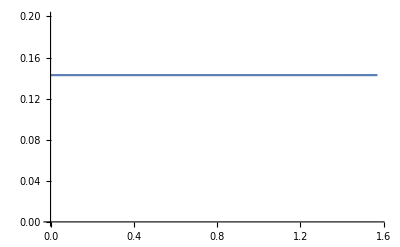

```mathematica
Plot[complexFresnel[x,0.0,0.25],{x,0,π/2},PlotRange->{0,0.2}]
```

```mathematica
Manipulate[Plot[complexFresnel[x,nx,ny]-complexFresnel[0,nx,ny],{x,0,π/2},PlotRange->{0,0.001}],{nx,0,1},{ny,0,1}]
```

```mathematica
relativeComplexFresnel=Function[{x,nx,ny},complexFresnel[x,nx,ny]-complexFresnel[0,nx,ny]];
```

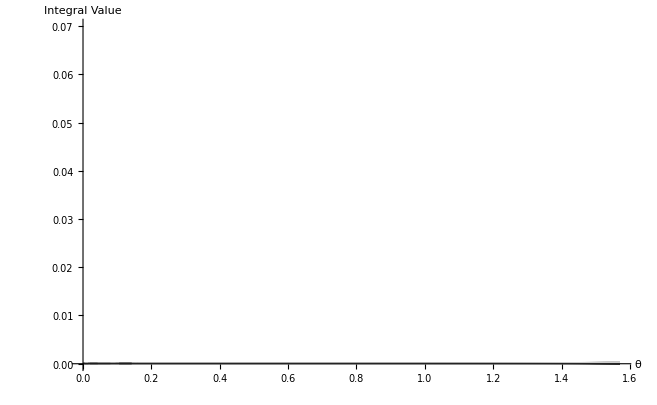

```mathematica
Show[Table[Plot[relativeComplexFresnel[x,nx,0.0],{x,0,π/2},PlotRange->{0,0.07},PlotStyle->GrayLevel[0.8*nx],AxesLabel->{"θ","Integral Value"}],{nx,0,1,0.1}]]
```

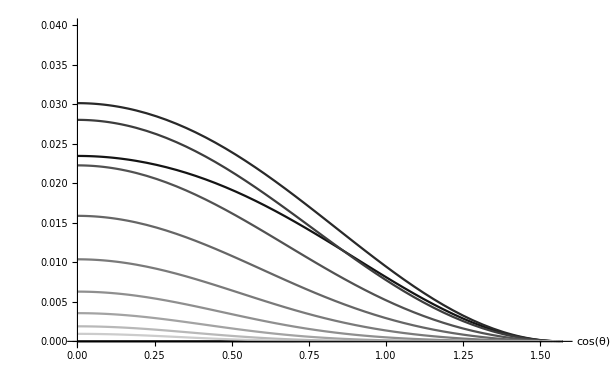

```mathematica
Show[Table[Plot[relativeComplexFresnel[Cos[x],0,ny],{x,0,π/2},PlotRange->{0,0.04},PlotStyle->GrayLevel[0.8*ny],AxesLabel->{"cos(θ)",""}],{ny,0,1,0.1}]]
```

```mathematica
Show[Table[Plot[relativeComplexFresnel[Cos[x],0,ny] / relativeComplexFresnel[Cos[x],0,0],{x,0,π/2},PlotRange->{0,0.5},PlotStyle->GrayLevel[0.8*ny],AxesLabel->{"cos(θ)",""}],{ny,0,1,0.1}]]
```

-Graphics-

```mathematica
Manipulate[Show[Table[Plot[relativeComplexFresnel[Cos[x],nx,ny] / relativeComplexFresnel[Cos[x],0,0],{x,nx,π/2},PlotRange->{{0,1},{0,1}},PlotStyle->GrayLevel[0.8*ny],AxesLabel->{"cos(θ)",""}],{ny,0,1,0.1}]],{nx,0,1}]
```

### Fitting the Ny factor

Let’s approximate the factor to the N_x=0 curve depending on the value of N_y:

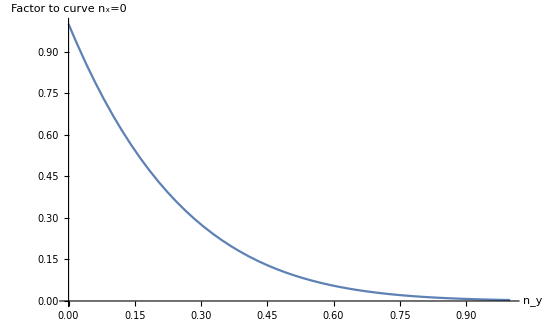

```mathematica
Plot[relativeComplexFresnel[1,0,ny] / relativeComplexFresnel[1,0,0],{ny,0,1},PlotRange->{0,1},AxesLabel->{"n_y","Factor to curve n_x=0"}]
```

{a→1.,b→5.99821,c→1.5708,d→1.}

Function[x,1.01589 (-0.0156444+2^(-5.99821 x))]

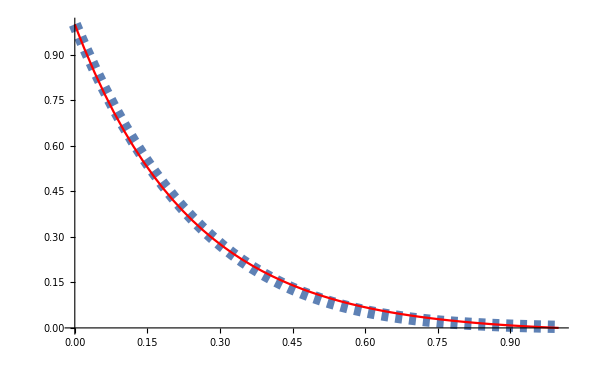

1.

```mathematica
taNy=Table[{ny,relativeComplexFresnel[1,0,ny] / relativeComplexFresnel[1,0,0]},{ny,0,1,0.01}];
ListPlot[taNy];
modelNy=1+b*x+c*x^2+d*x^3;
modelNy=1/(1+b*x+c*x^2+d*x^3);
modelNy=a*(2^(-b*x)-2^-b)/(a*(1-2^-b));
fitNy=FindFit[taNy,{modelNy},{a,b,{c,π/2},d},{x}]
funcNy=Function[x,Evaluate[modelNy/.fitNy]]
(*funcNy=Function[x,1-3.603488170946441 x+4.54559390006032 x^2-1.9574383454756639 x^3]
funcNy=Function[x,1-3.5* x+4.4* x^2-1.90* x^3]*)
Show[Plot[relativeComplexFresnel[1,0,x] / relativeComplexFresnel[1,0,0],{x,0,1},PlotRange->{0,1},PlotStyle->{Dashed, Thickness[0.015]}], Plot[funcNy[x],{x,0,1},PlotStyle->Red]]
funcNy[0]
```

### Plotting regular integral

Let’s plot the regular integral that isn’t dependent on the fresnel term:
	∫_θ_0^θ_1 (n'.ω'_i)sin(θ)dθ=n_x/2[θ_1-θ_0+sin(θ_0)cos(θ_0)- sin(θ_1)cos(θ_1)]+n_y/2[cos^2(θ_0)-cos^2(θ_1)]

```mathematica
Integrate[Cos[x]Sin[x],x]
Integrate[Sin[x]Sin[x],x]
```

-1/2 Cos[x]^2

x/2-1/4 Sin[2 x]

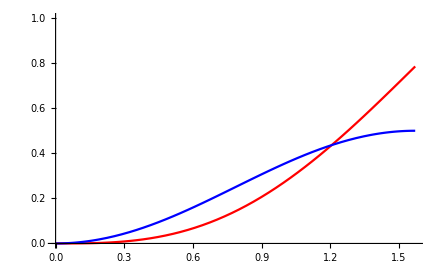

```mathematica
regularTermNx[x_]:=x/2-1/4 Sin[2 x]
regularTermNy[x_]:=-1/2 Cos[x]^2
Show[Plot[regularTermNx[x]-regularTermNx[0],{x,0,π/2},PlotRange->{0,1},PlotStyle->Red],
Plot[regularTermNy[x]-regularTermNy[0],{x,0,π/2},PlotRange->{0,1},PlotStyle->Blue]]
```

The red N_y term is pretty simple to estimate and already depends on cos(θ).
The blue N_x term is more problematic and involves an acos(θ) to retrieve the angle θ itself.
We could totally merge the complicated

### Assuming Ny always is √(1-Nx^2)

It’s a bad idea!

```mathematica
complexFresnel2=Function[{x,a},Evaluate[Integrate[(1-a*Sin[x]-√(1-a^2)*Cos[x])^5 Sin[x],x]]]
Manipulate[Plot[complexFresnel2[x,a]-complexFresnel2[0,a],{x,0,1},PlotRange->{0,0.5}],{a,0,1}]
```

Function[{x,a},1/192 (-1260 a x-72 (11+20 a^2) Cos[x]+45 √(1-a^2) (11+12 a^2) Cos[2 x]-220 Cos[3 x]+320 a^2 Cos[3 x]+160 a^4 Cos[3 x]+66 √(1-a^2) Cos[4 x]-252 a^2 √(1-a^2) Cos[4 x]-24 a^4 √(1-a^2) Cos[4 x]-12 Cos[5 x]+96 a^2 Cos[5 x]-96 a^4 Cos[5 x]+√(1-a^2) Cos[6 x]-12 a^2 √(1-a^2) Cos[6 x]+16 a^4 √(1-a^2) Cos[6 x]+1440 a √(1-a^2) Sin[x]+225 a Sin[2 x]+540 a^3 Sin[2 x]-400 a √(1-a^2) Sin[3 x]-160 a^3 √(1-a^2) Sin[3 x]+195 a Sin[4 x]-240 a^3 Sin[4 x]-24 a^5 Sin[4 x]-48 a √(1-a^2) Sin[5 x]+96 a^3 √(1-a^2) Sin[5 x]+5 a Sin[6 x]-20 a^3 Sin[6 x]+16 a^5 Sin[6 x])]

```mathematica
Manipulate[Plot[complexFresnel[x,a,√(1-a^2)]-complexFresnel[0,a,√(1-a^2)],{x,0,1},PlotRange->{0,0.5}],{a,0,1}]
```

### Blue-Noise Shadow Sampling

Blue-noise distribution of 64 samples generated by simply finding the 64 first pixels of a blue-noise texture...

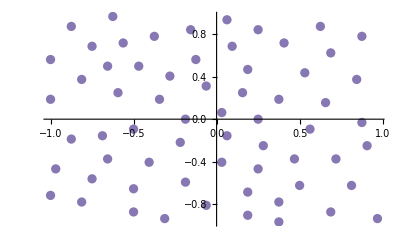

```mathematica
shadowSamples={{-0.75,0.6875},{0.1875,-0.6875},{-0.125,0.5625},{-0.8125,-0.78125},{-0.21875,-0.21875},{0.375,0.1875},{0.71875,-0.375},{0.40625,0.71875},{-0.3125,-0.9375},{0.84375,0.375},{0.6875,-0.875},{0.28125,-0.25},{-0.65625,-0.375},{-0.34375,0.1875},{0.0625,0.9375},{0.875,0.78125},{0.875,-0.03125},{0.03125,0.0625},{-0.1875,-0.59375},{-0.46875,0.5},{0.1875,0.46875},{-0.96875,-0.46875},{-0.5,-0.65625},{-0.8125,0.375},{0.5625,-0.09375},{0.375,-0.96875},{0.5,-0.625},{-0.625,0.96875},{0.53125,0.4375},{-0.5,-0.09375},{-0.375,0.78125},{0.03125,-0.40625},{-0.875,-0.1875},{0.96875,-0.9375},{0.65625,0.15625},{0.8125,-0.625},{-0.0625,0.3125},{0.625,0.875},{-0.0625,-0.8125},{-0.40625,-0.40625},{-1,0.5625},{-1,0.1875},{-0.59375,0.25},{0.6875,0.625},{0.09375,0.6875},{-0.15625,0.84375},{0.46875,-0.375},{-0.875,0.875},{0.25,0},{0.0625,-0.15625},{-0.1875,0},{0.90625,-0.25},{0.25,-0.46875},{0.15625,0.25},{-0.75,-0.5625},{-0.28125,0.40625},{0.25,0.84375},{-1,-0.71875},{-0.5,-0.875},{0.1875,-0.90625},{-0.5625,0.71875},{-0.6875,-0.15625},{-0.65625,0.5},{0.375,-0.78125},};
ListPlot[shadowSamples]
```